```mathematica
Clear["Global`*"];
```

```mathematica
refractiveIndex=Import["SMF28.xlsx", Path->NotebookDirectory[]][[1,2;;]];
nMat =1.444;
refractiveIndex[[All,2]]=refractiveIndex[[All, 2]]+nMat;
nCore=Mean[refractiveIndex[[369-1;;399-1,2]]];
nCladding1 = Mean[{Mean[refractiveIndex[[84-1;;354-1,2]]],Mean[refractiveIndex[[414-1;;684-1,2]]]}];
nCladding2 = Mean[{Mean[refractiveIndex[[2-1;;59-1,2]]],Mean[refractiveIndex[[709-1;;746-1,2]]]}];
ListPlot[refractiveIndex, PlotRange->All,ImageSize->Large,Joined->True];
```

```mathematica
refractiveIndexSymmetric = Join[
{{0,
2refractiveIndex[[384-1,2]]}},
Transpose[{2refractiveIndex[[385-1;;,1]],
Reverse[refractiveIndex[[22-1;;383-1,2]]]+refractiveIndex[[385-1;;,2]]}],
Transpose[{-2 Reverse[refractiveIndex[[2-1;;21-1,1]]],
2*Reverse[refractiveIndex[[2-1;;21-1,2]]]}]
]/2;
ListPlot[refractiveIndexSymmetric, PlotRange->All,ImageSize->Large,Joined->True];
```

```mathematica
maxN = 350;
rMax = refractiveIndexSymmetric[[maxN+1,1]];
NN = Length[refractiveIndexSymmetric[[2;;maxN+1,2]]];
λ = 0.55;
k0 = 2Pi/λ;
l = 1;
h = refractiveIndexSymmetric[[2,1]];
n = refractiveIndexSymmetric[[2;;maxN+1,2]];
rList = refractiveIndexSymmetric[[2;;maxN+1,1]];
rHyperbolic = 1/refractiveIndexSymmetric[[2;;maxN+1,1]];
```

```mathematica
D1=DiagonalMatrix[ConstantArray[-1/2,NN-1],-1]+DiagonalMatrix[ConstantArray[1/2,NN-1],1];
D1[[1]]=PadRight[{-3/2,2,-1/2},NN];
D1[[-1]]=PadLeft[{1/2,-2,3/2},NN];
D2=Normal[SparseArray[{Band[{1,1}]->-2,Band[{2,1}]->1,Band[{1,2}]->1},{NN,NN}]];
D2[[1]]=PadRight[{2,-5,4,-1},NN];
D2[[-1]]=PadLeft[{-1,4,-5,2},NN];
```

```mathematica
{β,Modes} = Eigensystem[D2/h^2 + D1 rHyperbolic / h -l^2 rHyperbolic^2 IdentityMatrix[NN] + k0^2 n^2 IdentityMatrix[NN]];
β=Chop[Sqrt[β]]/k0;
TrueModesNeff=Select[β,(Abs[Im[#]]≤10^-3&&nCladding1< Re[#]<nCore)&];
TrueModesNumber=Parallelize[Array[Position[β,TrueModesNeff[[#]]][[1,1]]&,Length[TrueModesNeff]]];
TrueModesNumber=Select[TrueModesNumber,(Chop[Max[Take[Modes[[#]],-50]]]/Chop[Max[Take[Modes[[#]],+50]]]≤10^-3)&];
TrueModes =Chop[Modes[[TrueModesNumber]]];
ListPlot[Abs[TrueModes[[;;]]],DataRange->{0,rMax}, PlotRange->All,Joined->True,ImageSize->Large];
```

```mathematica
NormModes = Parallelize[Array[
TrueModes[[#]]/Sqrt[NIntegrate[2Pi r (Interpolation[Transpose[{rList,Abs[TrueModes[[#]]]}],InterpolationOrder->1][r])^2,{r,0, rMax}]]
&,Length[TrueModes],1]];
```

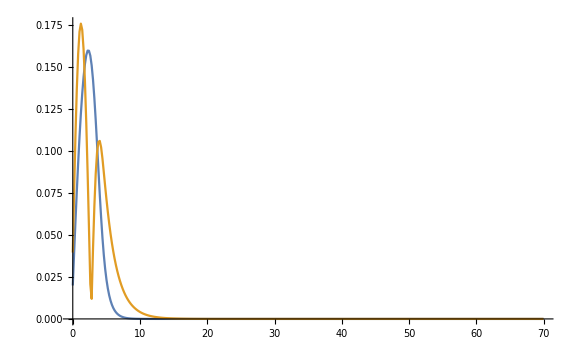

```mathematica
ListPlot[Abs[NormModes[[;;]]],PlotRange->All,DataRange->{0,rMax},Joined->True,ImageSize->Large]
```

```mathematica
NIntegrate[2Pi r (Interpolation[Transpose[{rList,Abs[NormModes[[1]]]}],InterpolationOrder->1][r])^2,{r,0, rMax}]==1;
```

```mathematica
Abs[NIntegrate[2 Pi rr×
(Interpolation[Transpose[{rList,NormModes[[1]]}],InterpolationOrder->1][rr])×(Interpolation[Transpose[{rList,Conjugate[NormModes[[Min[2,Length[NormModes]]]]]}],InterpolationOrder->1][rr])
,{rr,0,rMax}]]≤10^-3
```

True

```mathematica
Θ[θ_]=(((ΘΘ[θθ]/.DSolve[(-ΘΘ''[θθ])/ΘΘ[θθ]==l^2,ΘΘ[θθ],θθ])/.{C[1]->1,C[2]->0})[[1]])/.{θθ->θ};
```

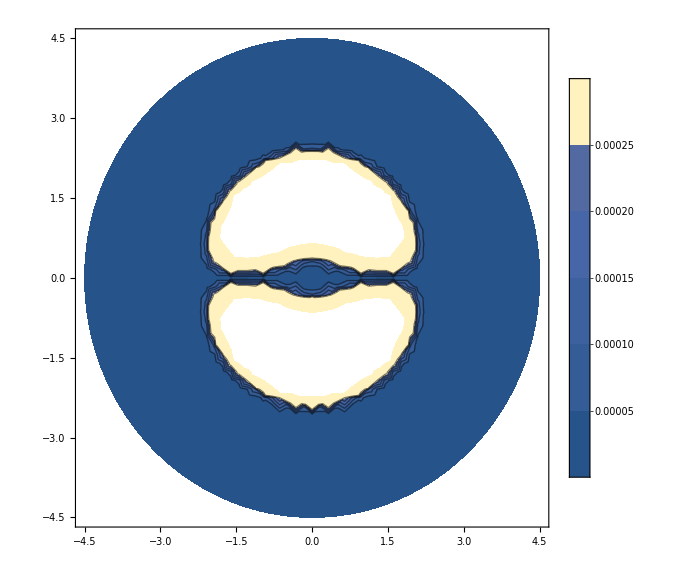

```mathematica
rCore = 3;
nShow = 1.5;
ContourPlot[(Abs[Θ[θ]×Interpolation[Transpose[{rList,NormModes[[1]]}],InterpolationOrder->1][r]])^2/.{r->x^2+y^2, θ->ArcTan[x/y]},{x,-nShow rCore,+nShow rCore},{y, -nShow rCore,+nShow rCore},
RegionFunction->Function[{x,y},x^2+y^2≤(nShow rCore)^2],PlotLegends->Automatic,ImageSize->Large]
```

```mathematica
ListPointPlot3D[Flatten[Parallelize[Table[{rr Cos[θ],rr Sin[θ],(Abs[Θ[θ]×Interpolation[Transpose[{rList,NormModes[[1]]}],InterpolationOrder->1][rr]])^2},
{rr,h,3rCore,h/5},{θ,0,2 Pi,2Pi/16}]],1],ImageSize->Large,PlotRange->All,ColorFunction->"TemperatureMap",Filling->None]
```

-Graphics3D-